### Start choosing the example:

```mathematica
t=26;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
v0={MFGEquations["jvars"],MFGEquations["jtvars"],MFGEquations["uvars"]}/.MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Done.

{0.018286,Null}

{<|{2,1->2}→80,{ex260,2->ex260}→80,{1,en259->1}→80,{1,1->2}→0,{2,2->ex260}→0,{en259,en259->1}→0|>,<|{1,1->2,en259->1}→0,{1,en259->1,1->2}→80,{2,1->2,2->ex260}→80,{2,2->ex260,1->2}→0|>,<|{1,1->2}→95,{2,2->ex260}→15,{en259,en259->1}→95,{2,1->2}→-80+95,{ex260,2->ex260}→15,{1,en259->1}→95|>}

```mathematica
KeySort@MFGEquations["criticalreduced2"][[2]]
MFGEquations["criticalreduced1"][[2]]//KeySort//Values
MFGEquations["criticalreduced2"][[2]]//KeySort//Values
```

<|j225→80,j226→80,j227→80,j228→0,j229→0,j230→0,jt231→0,jt232→80,jt233→80,jt234→0,u235→95,u236→15,u237→95,u238→-80+95,u239→15,u240→95|>

{80,80,80,0,0,0,0,80,80,0,95,15,95,15,15,95}

{80,80,80,0,0,0,0,80,80,0,95,15,95,15,15,95}

#### Non-linear case

```mathematica
Parameters["alpha"]=1;
```

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)];
v1=Values[nsol1//KeySort]
```

{80,80,80,0,0,0,0,80,80,0,95,15,95,15,15,95}

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)];
v2=Values@KeySort@nsol2
```

{80,80,80,0,0,0,0,80,80,0,95,15,95,15,15,95}

```mathematica
v0 //Values//N
v1//N
v2//N
```

{{80.,80.,80.,0.,0.,0.},{0.,80.,80.,0.},{95.,15.,95.,15.,15.,95.}}

{80.,80.,80.,0.,0.,0.,0.,80.,80.,0.,95.,15.,95.,15.,15.,95.}

{80.,80.,80.,0.,0.,0.,0.,80.,80.,0.,95.,15.,95.,15.,15.,95.}

### What is this plot for?

<|{2,1->2}→80,{1,1->2}→0|>

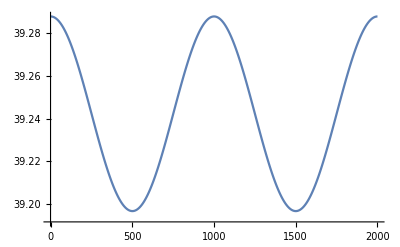
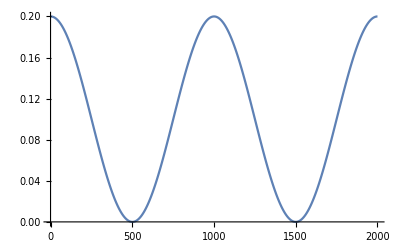
<|{2,1->2}→-Graphics-,{1,1->2}→-Graphics-|>

```mathematica
boel=Join[AtHead/@MFGEquations["BEL"],AtTail/@MFGEquations["BEL"]];
newstuff=AssociationThread[boel,MFGEquations["jvars"]/@boel];
jv=newstuff/.nsol2
Function[j,ListLinePlot [F[j,#]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

```mathematica
Parameters
```

<|alpha→1,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$17157[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$17157[x$]-g$17157[m$]]|>

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.